# Example evaluation for package of TMD packages

```mathematica
SetOptions[$Output⟦1⟧,FormatType->StandardForm]
```

{BinaryFormat→False,FormatType→StandardForm,PageWidth→79,PageHeight→22,TotalWidth→∞,TotalHeight→∞,CharacterEncoding:>Unicode,NumberMarks:>$NumberMarks,Method→{File,BinaryFormat→False}}

## AlphaStrong

```mathematica
SetDirectory[NotebookDirectory[]];
<<AlphaStrong`
```

Package AlphaStrong for evaluation of as[μ]=g^2/(4 π)^2, at 1-,2-,3- loops.

Contains the following functions: as[n,μ], asIt[n,μ], ΛQCD[n,μ], ActiveN[μ], As[n,m,μ,μ0], AsLog[n,m,μ,μ0]

Contains the following anomalous dimensions: β0[Nf], β1[Nf], β2[Nf], β3[Nf]

Contains the following constants: mBOTTOM, mCHARM

Copyright: Alexey Vladimirov, Regensburg University. Version 1.101 (1 Sep. 2016)

___________________________________________________________________________

```mathematica
?as
```

as[n_Integer,μ_Number]  returns as=g^2/(4 π)^2 for n-loops and μ-scale.
Here the (standard) HEP solution is used. This solution is rather weakly approximate an exact solution, but it is commonly used. Since it is the standard, it is preferable, and better normalized.
as[MZ]=asMSTW2008. + threashold matching.

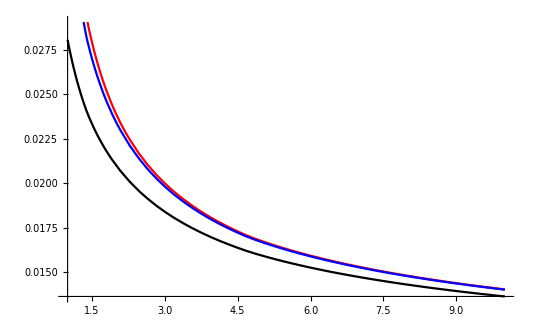

```mathematica
Plot[{as[1,μ],as[2,μ],as[3,μ]},{μ,1.,10},PlotStyle->{Black,Red,Blue}]
```

```mathematica
?asIt
```

asIt[n_Integer,μ_Number]  returns as=g^2/(4 π)^2 for n-loops and μ-scale.
Here the double iteractive solution is used. The double iterative solution is very close to an exact solution, but it give non-common Λ's, since the standard fits uses the HEP solution.
asIt[MZ]=asMSTW2008. + threashold matching.

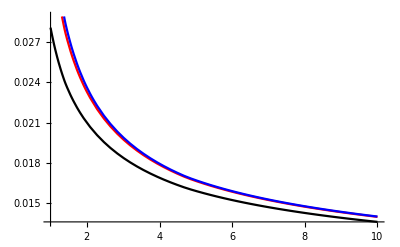

```mathematica
Plot[{asIt[1,μ],asIt[2,μ],asIt[3,μ]},{μ,1.,10},PlotStyle->{Black,Red,Blue}]
```

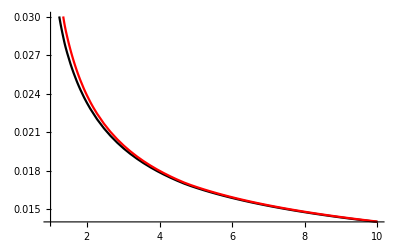

```mathematica
Plot[{asIt[2,μ],as[2,μ]},{μ,1.,10},PlotStyle->{Black,Red,Blue}]
```

## TMDevolution

```mathematica
SetDirectory[NotebookDirectory[]];
<<TMDevolution`
```

Package TMDevolution contains the set of functions related to the TMD-evolution kernel R

Load package AlphaStrong

Contains the following functions: Cf, bstar, Dboundary, Γevolutor, ΓLogevolutor, γevolutor, RTMD, RTMD2

Contains the following anomalous dimensions: Γcusp, Γc, γV, ddTMD, dd

Copyright: Alexey Vladimirov, Regensburg University. Version 1.501 (1 Sep. 2016)

___________________________________________________________________________

## Anomalous Dimensions

```mathematica
?Γcusp
```

Γcusp[f_,n_,Nf_] the coefficeint of the cusp anomalous dimension at as^n.
Nf is the number of active quarks.
f is a flavour. It can be "q" for quark and anti-quark, or "g" for gluon

```mathematica
Γcusp["q",3,Nf]
```

16/3 (735/2-(4 Nf^2)/27-(134 π^2)/3+(11 π^4)/5+1/9 Nf (-319+20 π^2-156 Zeta[3])+66 Zeta[3])

```mathematica
{γV["g",1,3],γV["g",1,4],γV["g",1,5]}//N//InputForm
```

{-18., -16.666666666666668, -15.333333333333334}

```mathematica
γV["g",1,Nf]
```

-22+(4 Nf)/3

```mathematica
?γV
```

γV[f_,n_,Nf_]  the part coefficeint of the TMD anomalous dimension at as^n.
Anomalous dimension defined as (d\ F)/(d\ ln\ SuperscriptBox[μ, 2])=γ/2F,  where γ=Γcusp ln(mu^2/ζ)-γV. This defines γV.
Nf is the number of active quarks.
f is a flavour. It can be "q" for quark and anti-quark, or "g" for gluon.

```mathematica
?ddTMD
```

dTMD[f_,n_,k_,Nf_] the coefficeint for rapidity anomalous dimension D at as^nLμ^k.
f is a flavour. It can be "q" for quark and anti-quark, or "g" for gluon.
It is defined as (see also dd) (d\ F)/(d\ ln\ ζ)=- D F, where D=C_f dd.

```mathematica
?dd
```

dd[n_,k_,Nf_]  flavour independent the coefficeint for rapidity anomalous dimension D at as^nLμ^k.
It is defined as (d\ F)/(d\ ln\ ζ)=- D F, where D=C_f dd.
Nf is the number of active quarks.

```mathematica
ddTMD["q",3,2,Nf]
dd[3,2,Nf]
```

4/3 (102-(38 Nf)/3+2 (11-(2 Nf)/3) (67/3-(10 Nf)/9-π^2))

102-(38 Nf)/3+2 (11-(2 Nf)/3) (67/3-(10 Nf)/9-π^2)

```mathematica
?ΓLogevolutor
```

ΓLogevolutor[f_,n_,μ_,μ0_] the evolution integral for double-logs.
(∫_μ0)^μdν/νΓ[as[ν]] Log[ν^2/μ0^2] at n-loop order. 
f is for flavor.
USES AsLog

```mathematica
?AsLog
```

AsLog[n_,m_,  μ_, μ0_]  is\ the\ function\ defined\ as\ OverscriptBox[SubscriptBox[∫, μ0], μ]FractionBox[dν, ν] SuperscriptBox[as[m, ν], n]Log[ν^2/μ0^2].
It uses default definition of as.
IMPORTANT: MEMORY-CONSUMING the function self-memorize the evaluated values. We have done it in order to speed up calculation, since these values are often-used functions. The procedure it sefl is not very memory-consuming, basically every point is 4-real numbers.
None the less we recommend to evaluate functions controlably, i.e. point-by-point, since uncontrolable evaluation (e.g. functions like Plot) can generate many useless data. It is also convinient to use Share[AsLog] from time to time, it reduces the memory usage.
In the case of sirious memory-leak coused by function As use Clear[AsLog], and restart  package.

## Evolution integrals

```mathematica
?Γevolutor
```

Γevolutor[f_,n_,μ_,μ0_] the evolution integral defined as
(∫_μ0)^μdν/νΓ[as[ν]] at n-loop order.
f is for flavor of D.
USES As

It is not defined for μ0<Λ. And, thus, gives mistakes.

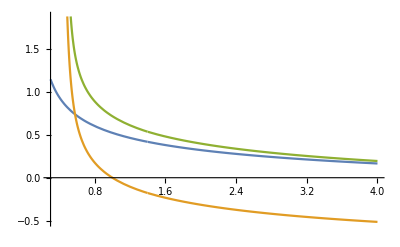
{0.071659,-Graphics-}

```mathematica
Plot[{Γevolutor["g",1,10,μ0],Γevolutor["g",2,1,μ0],Γevolutor["g",3,10,μ0]},{μ0,0.3,4}]//Timing
```

```mathematica
Γevolutor["g",3,10,0.02]
```

7.38952×10^29

First time evaluation takes some time for tabulating intrinsic variables

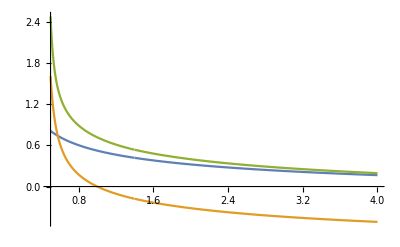
{0.047603,-Graphics-}

```mathematica
Plot[{Γevolutor["g",1,10,μ0],Γevolutor["g",2,1,μ0],Γevolutor["g",3,10,μ0]},{μ0,0.5,4}]//Timing
```

But next evaluations takes much-much less time.

```mathematica
Plot[{Γevolutor["g",1,10,μ0],Γevolutor["g",2,1,μ0],Γevolutor["g",3,10,μ0]},{μ0,0.5,4}]//Timing
```

{0.044937,-Graphics-}

```mathematica
?DTMD
```

DTMD[f_,n_,μ_,bt_,μ0_] the rapirity anomalous dimension D. 
Defined as (d\ F)/(d\ ln\ ζ)=- D F. DTMD=Γevolutor+Dboundary.
n is order of evaluation, f is flavor, μ is high-energy parameter, bt is bt, μ0 is low-energy parameter (see documentatio)

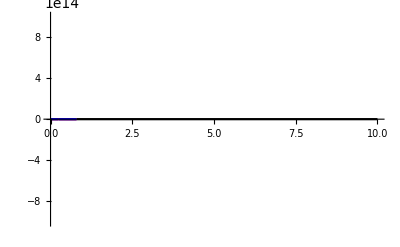
{1.47908,-Graphics-}

```mathematica
Plot[{DTMD["g",1,10,bt,C0/bt],DTMD["g",2,10,bt,C0/bt],DTMD["g",3,10,bt,C0/bt]},{bt,0,10},PlotStyle->{Black,Red,Blue}]//Timing
```

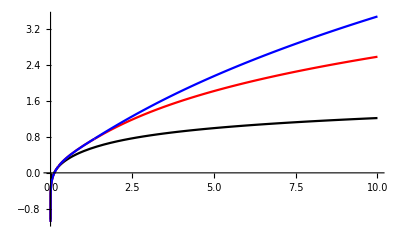
{0.124535,-Graphics-}

```mathematica
Plot[{DTMD["g",1,10,bt,C0/bstar[bt,1]],DTMD["g",2,10,bt,C0/bstar[bt,1]],DTMD["g",3,10,bt,C0/bstar[bt,1]]},{bt,0,10},PlotStyle->{Black,Red,Blue}]//Timing
```

```mathematica
?ΓLogevolutor
```

ΓLogevolutor[f_,n_,μ_,μ0_] the evolution integral for double-logs.
(∫_μ0)^μdν/νΓ[as[ν]] Log[ν^2/μ0^2] at n-loop order. 
f is for flavor.
USES AsLog

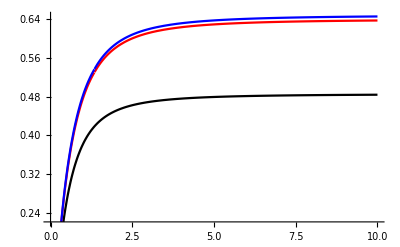
{0.105603,-Graphics-}

```mathematica
Plot[{Γevolutor["g",1,10,C0/bstar[bt,1]],Γevolutor["g",2,10,C0/bstar[bt,1]],Γevolutor["g",3,10,C0/bstar[bt,1]]},{bt,0,10},PlotStyle->{Black,Red,Blue}]//Timing
```

```mathematica
?γevolutor
```

γevolutor[f_,n_,μ_,μ0_] the evolution integral for TMD anomalous dimension γV.
(∫_μ0)^μdν/νγV[as[ν]] at n-loop order.
f is for flavor.
USES As.

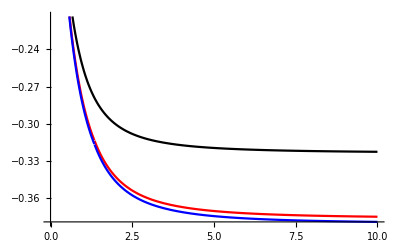
{0.219219,-Graphics-}

```mathematica
Plot[{γevolutor["q",1,10,C0/bstar[bt,1]],γevolutor["q",2,10,C0/bstar[bt,1]],γevolutor["q",3,10,C0/bstar[bt,1]]},{bt,0,10},PlotStyle->{Black,Red,Blue}]//Timing
```

```mathematica
?DTMD
```

DTMD[f_,n_,μ_,bt_,μ0_] the rapirity anomalous dimension D. 
Defined as (d\ F)/(d\ ln\ ζ)=- D F. DTMD=Γevolutor+Dboundary.
n is order of evaluation, f is flavor, μ is high-energy parameter, bt is bt, μ0 is low-energy parameter (see documentatio)

```mathematica
?Dboundary
```

Dboundary[f_,n_,μ_,bt_] pertrubative value of the rapirity anomalous dimension D. 
Used as a boundary for anomalous dimension D at μ0.

## Evolution Kernel R

```mathematica
?RTMD
```

RTMD[f_,n_,bt_,ζf_,μf_,ζi_,μi_,μ0_] the TMD evolution kernel. 
Defined as Exp[(∫_μi)^μfdμ/μγ[μ,ζf]]Exp[-D[μi,bt]Log[ζf/ζi].
The parameter f("q" of "g") is flavour.
The parameter μ0 is low-energy behaviour of function D.
The following verions of function exists:
RTMD[f,n,bt,ζf,μf,μi,μ0] ζi=ζb=C0^2/bt^2 
RTMD[f,n,bt,ζf,μf,μ0] ζi=ζb=C0^2/bt^2, μi=μ0

```mathematica
RTMD["q",3,5,10,9.3,0.9]
```

0.0197527

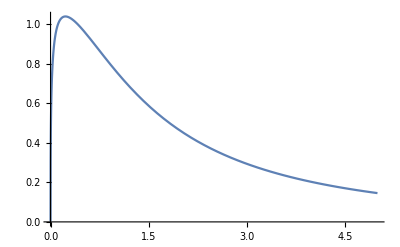
{1.63812,-Graphics-}

```mathematica
Timing[Plot[RTMD["q",1,bt,10.^2,10.,C0/bstar[bt,1.]],{bt,0,5}]]
```

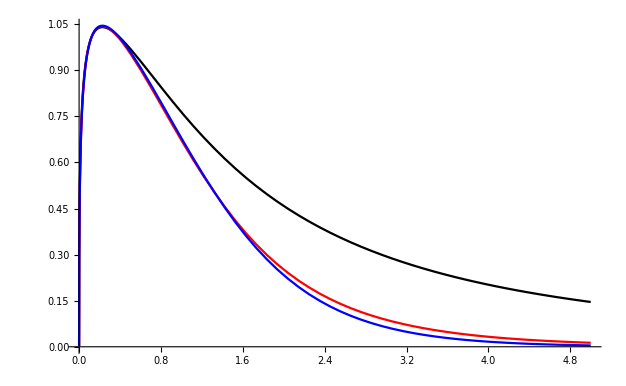

```mathematica
Plot[{RTMD["q",1,bt,10.^2,10.,C0/bstar[bt,1.]],RTMD["q",2,bt,10.^2,10.,C0/bstar[bt,1.]],RTMD["q",3,bt,10.^2,10.,C0/bstar[bt,1.]]},{bt,0,5},PlotStyle->{Black,Red,Blue}]
```

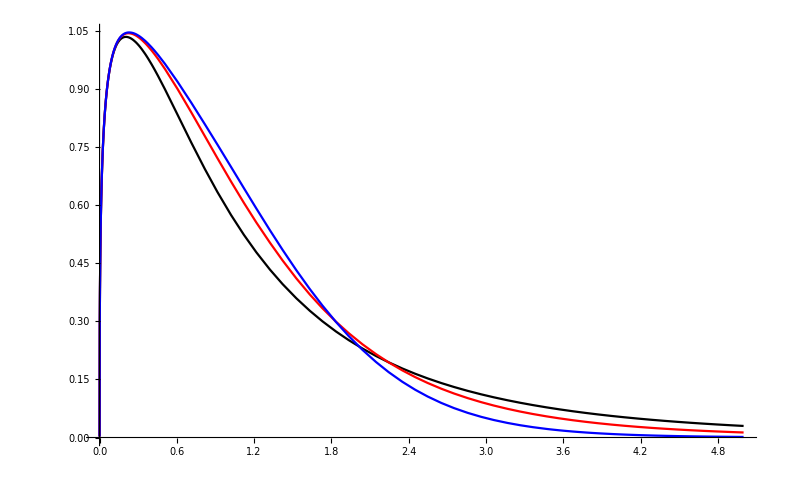

```mathematica
Plot[{RTMD["q",2,bt,10.^2,10.,C0/bstar[bt,0.5]],RTMD["q",2,bt,10.^2,10.,C0/bstar[bt,1.]],RTMD["q",2,bt,10.^2,10.,C0/bstar[bt,1.5]]},{bt,0,5},PlotStyle->{Black,Red,Blue}]
```

```mathematica
?RTMD2
```

RTMD2[f_,pn_,bt_,ζf_,μf_,ζi_,μi_,μ0_] the TMD evolution kernel over the alternative contour. 
Defined as Exp[(∫_μi)^μfdμ/μγ[μ,ζi]]Exp[-D[μf,bt]Log[ζf/ζi].
The parameter f("q" of "g") is flavour.
The parameter μ0 is low-energy behaviour of function D.
The following verions of function exists:
RTMD2[f,n,bt,ζf,μf,μi,μ0] ζi=ζb=C0^2/bt^2 
RTMD2[f,n,bt,ζf,μf,μ0] ζi=ζb=C0^2/bt^2

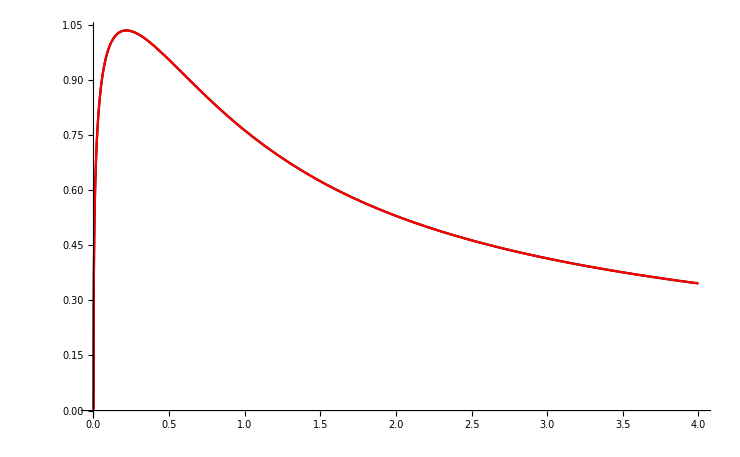

```mathematica
Plot[{RTMD2["q",1,bt,10.^2,10.,1.2,C0/bstar[bt,1.],C0/bstar[bt,1.]],RTMD2["q",1,bt,10.^2,10.,1.2,C0/bstar[bt,1.],C0/bstar[bt,1.]]},{bt,0,4},PlotStyle->{Black,Red},Filling->{1->{2}}]
```

## TMD at small - bt

DO NOT Forget to load MSTW!

```mathematica
SetDirectory[NotebookDirectory[]];
<<mstwpdf.m
```

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

```mathematica
Timing[ReadPDFGrid["./Grids/mstw2008nnlo",0]]
```

PDF grid read from ./Grids/mstw2008nnlo.00.dat

{5.62762,Null}

```mathematica
SetDirectory[NotebookDirectory[]];
<<TMDmatching`
```

Package TMDmatching contains the set of functions related to the TMD small-bT matching

Uses package AlphaStrong

REQUARES MSTW package and preloaded grids! They are used as input for the convoluitons.

Contains the following functions: CxF, CxFexp, CxFrenormalon, CxFrenormalonExp

Copyright: Alexey Vladimirov, Regensburg University. Version 1.201 (8 Sep. 2016)

___________________________________________________________________________

### Looking at TMD

```mathematica
CxF[0,1,"direct",10^-3,1.,10.]
CxF[1,1,"direct",10^-3,1.,10.]
CxF[2,1,"direct",10^-3,1.,10.]
```

997.06

1655.58

2073.17

```mathematica
CxF[0,1,"withMIX",10^-3,1.,10.]
CxF[1,1,"withMIX",10^-3,1.,10.]
CxF[2,1,"withMIX",10^-3,1.,10.]
```

997.06

1227.05

1204.01

```mathematica
CxF[0,0,"direct",10^-3,1.,10.]
CxF[1,0,"direct",10^-3,1.,10.]
CxF[2,0,"direct",10^-3,1.,10.]
```

16795.

25917.4

27866.8

```mathematica
CxF[0,0,"withMIX",10^-3,1.,10.]
CxF[1,0,"withMIX",10^-3,1.,10.]
CxF[2,0,"withMIX",10^-3,1.,10.]
```

16795.

22021.1

18887.1

```mathematica
NIntegrate[(-2 (-1+z) z+Lμ (-1+2 z-2 z^2))xf[0,x/z,10,0]/.{x->10.^-3,Lμ->%51},{z,10^-3,1},PrecisionGoal->5]
```

NIntegrate::inumr: The integrand (-2 (-1+z) z+Null (-1+2 z-2 z^2)) xf[0,0.001/z,10,0] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1/1000,1}}.

{NIntegrate[(-2 (-1+z) z+Null (-1+2 z-2 z^2)) xf[0,0.001/z,10,0],{z,1/10^3,1},PrecisionGoal→5]}

```mathematica
(-2 (-1+z) z+Lμ (-1+2 z-2 z^2))-(-Lμ+2(1+Lμ)z)//Simplify
```

-2 (1+Lμ) z^2

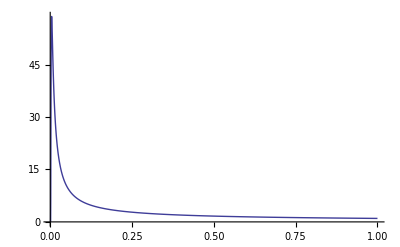

```mathematica
Plot[1/z xf[0,0.001/z,10,1],{z,0.001,1},PlotRange->All]
```

```mathematica
?CxF
```

CxF[n_,f_,type_,x_,bt_,μ_] is the leading order of the small-bT expansion for unpolirized TMD PDF.
It is defined as C_(q ← f)(bt,μ)⊗q_f)[x,μ].
The function uses MSTW2008 PDF as input.
n -- pertrubative order of coefficient function,
f -- parton flavour, defined as in MSTW2008, i.e. (-3,-2,-1,0,1,2,3)→ (sbar,ubar,dbar,gluon,d,u,s)
type -- defines inclusion or exclusion of parton mixture, "direct" no parton mixture terms, "withMIX" all terms, "onlyMIX" only mixture terms.
x, bt, μ -- usual TMD variables.
Function CxF[n_,f_,x_,bt_,μ_] evaluates matching without mixing. 
NOTE: parameter ζ is set to ζb (i.e. the ζ-logarithms exponentiated out), NF=3 for all coefficeints, for α_s we take 2-loop definition irrespective pertrubtive order.
ANOTHER NOTE: we use PrecisionGoal→5, since it speeds up the calculation, but far within errorband.

```mathematica
CxF[2,1,"withMIX",0.3,0.2,10.]
CxF[2,0,"withMIX",0.3,0.2,10.]
```

0.712681

0.777654

Since evaluation of convolutions is time-consuming, we suggest to evaluate point-by-point.

```mathematica
<<TMDevolution`
```

Package TMDevolution contains the set of functions related to the TMD-evolution kernel R

Load package AlphaStrong

Contains the following functions: Cf, bstar, Dboundary, Γevolutor, ΓLogevolutor, γevolutor, RTMD, RTMD2

Contains the following anomalous dimensions: Γcusp, Γc, γV, ddTMD, dd

Copyright: Alexey Vladimirov, Regensburg University. Version 1.501 (1 Sep. 2016)

___________________________________________________________________________

```mathematica
Timing[A1=Table[{x,x CxF[2,1,"withMIX",x,1,C0/bstar[1,1]]},{x,10^-6,0.3,0.001}];]
Timing[A2=Table[{x,x CxF[2,2,"withMIX",x,1,C0/bstar[1,1]]},{x,10^-6,0.3,0.001}];]
Timing[A3=Table[{x,x CxF[2,3,"withMIX",x,1,C0/bstar[1,1]]},{x,10^-6,0.3,0.001}];]
```

{220.886,Null}

{215.821,Null}

{198.892,Null}

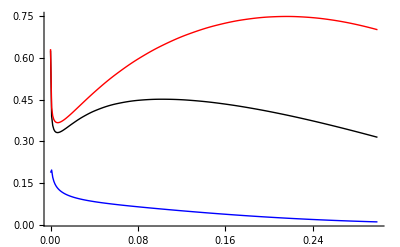

```mathematica
ListPlot[{A1,A2,A3},PlotStyle->{Black,Red,Blue},Joined->True]
```

The effect of mixing is very small, by evaluating it takes tons of time. If “withMIX” is not set, the mixing is not evaluated.

```mathematica
Timing[A1=Table[{x,x CxF[2,1,"direct",x,1,C0/bstar[1,1]]},{x,10^-6,0.3,0.001}];]
Timing[A2=Table[{x,x CxF[2,2,"direct",x,1,C0/bstar[1,1]]},{x,10^-6,0.3,0.001}];]
Timing[A3=Table[{x,x CxF[2,3,"direct",x,1,C0/bstar[1,1]]},{x,10^-6,0.3,0.001}];]
```

{28.3778,Null}

{30.8219,Null}

{25.7056,Null}

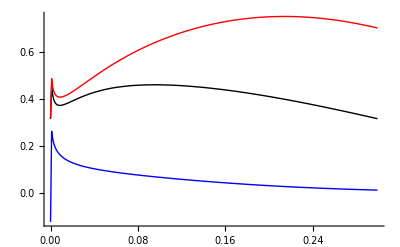

```mathematica
ListPlot[{A1,A2,A3},PlotStyle->{Black,Red,Blue},Joined->True]
```

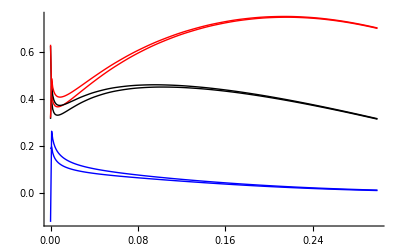

```mathematica
Show[%15,%19]
```

```mathematica
Timing[A1=Table[{bt,CxF[1,1,0.01,bt,C0/bstar[bt,1]]},{bt,10^-4,4,0.1}];]
Timing[A2=Table[{bt,CxF[1,2,0.01,bt,C0/bstar[bt,1]]},{bt,10^-4,4,0.1}];]
Timing[A3=Table[{bt,CxF[1,3,0.01,bt,C0/bstar[bt,1]]},{bt,10^-4,4,0.1}];]
```

{1.89212,Null}

{1.72811,Null}

{1.16407,Null}

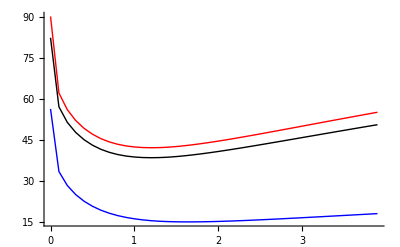

```mathematica
ListPlot[{A1,A2,A3},PlotStyle->{Black,Red,Blue},Joined->True]
```

```mathematica
Timing[A1=Table[{bt,CxF[0,0,0.01,bt,C0/bstar[bt,1]]},{bt,10^-4,4,0.1}];]
Timing[A2=Table[{bt,CxF[1,0,0.01,bt,C0/bstar[bt,1]]},{bt,10^-4,4,0.1}];]
Timing[A3=Table[{bt,CxF[2,0,0.01,bt,C0/bstar[bt,1]]},{bt,10^-4,4,0.1}];]
```

{0.016001,Null}

{2.75617,Null}

{12.2128,Null}

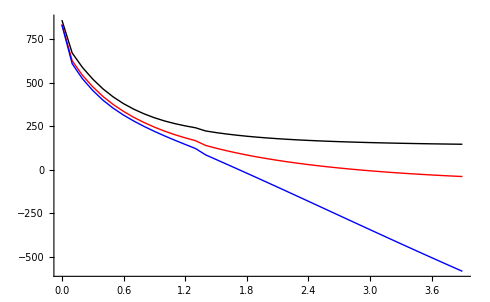

```mathematica
ListPlot[{A1,A2,A3},PlotStyle->{Black,Red,Blue},Joined->True]
```

```mathematica
Timing[A1=Table[{bt,CxF[0,2,0.01,bt,C0/bstar[bt,1]]},{bt,10^-4,4,0.1}];]
Timing[A2=Table[{bt,CxF[1,2,0.01,bt,C0/bstar[bt,1]]},{bt,10^-4,4,0.1}];]
Timing[A3=Table[{bt,CxF[2,2,0.01,bt,C0/bstar[bt,1]]},{bt,10^-4,4,0.1}];]
```

{0.012001,Null}

{1.75611,Null}

{5.86037,Null}

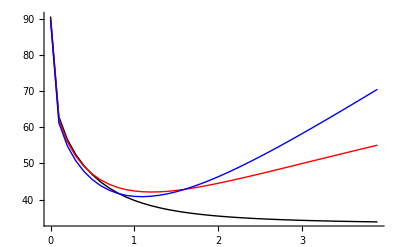

```mathematica
ListPlot[{A1,A2,A3},PlotStyle->{Black,Red,Blue},Joined->True]
```

```mathematica
A1=Table[{x,bt,x CxF[1,2,x,bt,C0/bstar[bt,1]]},{x,10^-3,1,0.025},{bt,10^-4,4,0.3}];//Timing
A2=Table[{x,bt,x CxF[2,2,x,bt,C0/bstar[bt,1]]},{x,10^-3,1,0.025},{bt,10^-4,4,0.3}];//Timing
```

{13.5048,Null}

{52.7353,Null}

```mathematica
ListPlot3D[{Flatten[A1,1]},AxesLabel->{"x","bt"},PlotRange->{0,2},InterpolationOrder->3]
ListPlot3D[{Flatten[A2,1]},AxesLabel->{"x","bt"},PlotRange->{0,2},InterpolationOrder->3]
```

-Graphics3D-

-Graphics3D-

```mathematica
ListPointPlot3D[{Flatten[A1,1],Flatten[A2,1]},AxesLabel->{"x","bt"}]
```

-Graphics3D-

### Looking at TMD renormalon correction

```mathematica
?CxFrenormalon
```

CxFrenormalon[f_,x_,bt_,μ_,Λ_] is the leading renormalon contribution to the quark TMD, without NUMERIC prefactor
It is defined as bt^2Λ^2 C_renormalon⊗ q.
The function uses MSTW2008 PDF as input.
f -- parton flavour (can be only quark, or anti quark), defined as in MSTW2008, i.e. (-3,-2,-1,0,1,2,3)→ (sbar,ubar,dbar,gluon,d,u,s)
x, bt, μ -- usual TMD variables.
Λ is the position of Landau pole, to which the divergent series summed. If not specified the 2-loop ΛQCD from the package AlphaStrong is used.

```mathematica
Timing[R1=Table[{bt,CxFrenormalon[1,0.01,bt,C0/bstar[bt,1]]},{bt,10^-4,4,0.1}];]
```

{0.696044,Null}

```mathematica
Timing[A1=Table[{bt,CxF[1,1,0.01,bt,C0/bstar[bt,1]]},{bt,10^-4,4,0.1}];]
```

{1.91212,Null}

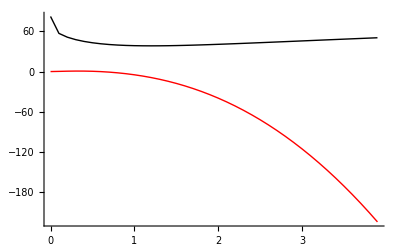

```mathematica
ListPlot[{A1,R1},PlotStyle->{Black,Red,Blue},Joined->True]
```

```mathematica
Timing[A1=Table[{x,-1.2CxFrenormalon[1,x,1,C0/bstar[1,1]]},{x,10^-6,1,0.001}];]
```

{24.9016,Null}

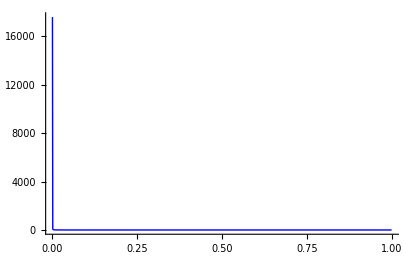

```mathematica
ListPlot[A1,PlotStyle->{Black,Red,Blue},Joined->True]
```

```mathematica
?CxFexp
```

CxFexp[n_,f_,type_,x_,bt_,μ_,g_] is the leading order of the small-bT expansion for unpolirized TMD PDF with exponential factor.
It is defined as C_(q ← f)(bt,μ)Exp[-x g bt^2]⊗q_f)[x,μ].
The function uses MSTW2008 PDF as input.
n -- pertrubative order of coefficient function,
f -- parton flavour, defined as in MSTW2008, i.e. (-3,-2,-1,0,1,2,3)→ (sbar,ubar,dbar,gluon,d,u,s)
type -- defines inclusion or exclusion of parton mixture, "direct" no parton mixture terms, "withMIX" all terms, "onlyMIX" only mixture terms.
x, bt, μ -- usual TMD variables.
g is the parameter of the exponent.
Function CxFexp[n_,f_,x_,bt_,μ_,g_] evaluates matching without mixing. 
NOTE: parameter ζ is set to ζb (i.e. the ζ-logarithms exponentiated out), NF=3 for all coefficeints, for α_s we take 2-loop definition irrespective pertrubtive order.
ANOTHER NOTE: we use PrecisionGoal→5, since it speeds up the calculation, but far within errorband.

```mathematica
Timing[A1=Table[{x,x CxF[1,2,"withMIX",x,1,C0/bstar[1,1]]},{x,10^-6,1,0.01}];]
Timing[A2=Table[{x,x CxF[2,2,"withMIX",x,1,C0/bstar[1,1]]},{x,10^-6,1,0.01}];]
```

{4.24026,Null}

{62.0799,Null}

```mathematica
Timing[B1=Table[{x,x CxFexp[1,2,"withMIX",x,1,C0/bstar[1,1],0.15815688133371278]},{x,10^-6,1,0.01}];]
Timing[B2=Table[{x,x CxFexp[2,2,"withMIX",x,1,C0/bstar[1,1],0.15815688133371278]},{x,10^-6,1,0.01}];]
```

{4.92831,Null}

{63.908,Null}

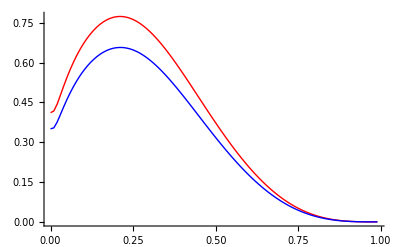

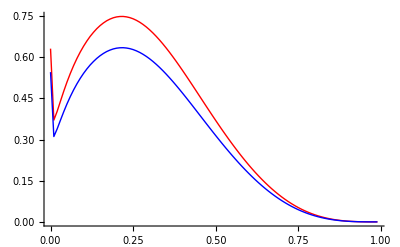

```mathematica
ListPlot[{A1,B1},PlotStyle->{Red,Blue},Joined->True]
ListPlot[{A2,B2},PlotStyle->{Red,Blue},Joined->True]
```

```mathematica
Timing[A1=Table[{bt,CxFexp[1,2,0.1,bt,C0/bstar[bt,1],0.158]},{bt,10^-3,6,0.1}];]
Timing[A2=Table[{bt,CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.158]},{bt,10^-3,6,0.1}];]
```

{2.60416,Null}

{7.83249,Null}

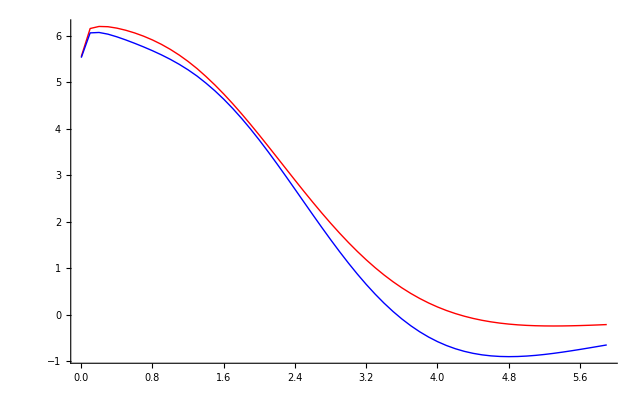

```mathematica
ListPlot[{A1,A2},PlotStyle->{Red,Blue},Joined->True]
```

```mathematica
Timing[A1=Table[{bt,CxF[2,2,0.1,bt,C0/bstar[bt,1]]},{bt,10^-3,6,0.1}];]
Timing[A2=Table[{bt,CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.0]},{bt,10^-3,6,0.1}];]
```

{6.82043,Null}

{6.84843,Null}

```mathematica
Total[A1-A2]
```

{0.,0.}

```mathematica
Timing[A1=Table[{bt,CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.0]},{bt,10^-3,6,0.1}];]
Timing[A2=Table[{bt,CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.05]},{bt,10^-3,6,0.1}];]
Timing[A3=Table[{bt,CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.1]},{bt,10^-3,6,0.1}];]
Timing[A4=Table[{bt,CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.15]},{bt,10^-3,6,0.1}];]
Timing[A5=Table[{bt,CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.2]},{bt,10^-3,6,0.1}];]
```

{6.88443,Null}

{8.37652,Null}

{7.9125,Null}

{7.9485,Null}

{7.60448,Null}

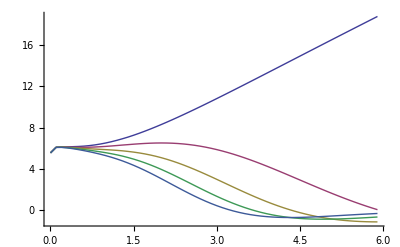

```mathematica
ListPlot[{A1,A2,A3,A4,A5},Joined->True]
```

```mathematica
?CxFrenormalonExp
```

CxFrenormalonExp[f_,x_,bt_,μ_,Λ_,g1_,g2_] is the leading renormalon contribution to the quark TMD, without NUMERIC prefactor, with the extra expoenential
It is defined as bt^2g1(*SubscriptBox[(C), (renormalon)])Exp[-x g2 bt^2] ⊗ q.
The discripancy of parameters is taken into account within the renormalon mathing.
The function uses MSTW2008 PDF as input.
f -- parton flavour (can be only quark, or anti quark), defined as in MSTW2008, i.e. (-3,-2,-1,0,1,2,3)→ (sbar,ubar,dbar,gluon,d,u,s)
x, bt, μ -- usual TMD variables.
Λ is the position of Landau pole, to which the divergent series summed. If not specified the 2-loop ΛQCD from the package AlphaStrong is used.

```mathematica
Timing[B1=Table[{bt,CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.1,0.0]},{bt,10^-3,6,0.1}];]
Timing[B2=Table[{bt,CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.1,0.01]},{bt,10^-3,6,0.1}];]
Timing[B3=Table[{bt,CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.1,0.02]},{bt,10^-3,6,0.1}];]
Timing[B4=Table[{bt,CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.1,0.03]},{bt,10^-3,6,0.1}];]
Timing[B5=Table[{bt,CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.1,0.04]},{bt,10^-3,6,0.1}];]
```

{1.5161,Null}

{1.6521,Null}

{1.76811,Null}

{1.85211,Null}

{1.92012,Null}

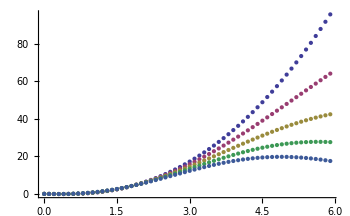

```mathematica
ListPlot[{B1,B2,B3,B4,B5}]
```

```mathematica
Timing[A1=Table[{bt,0.1(CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.0]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.1,0.0])},{bt,10^-3,6,0.1}];]
Timing[A2=Table[{bt,0.1(CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.03]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.1,0.03])},{bt,10^-3,6,0.1}];]
Timing[A3=Table[{bt,0.1(CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.06]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.1,0.06])},{bt,10^-3,6,0.1}];]
Timing[A4=Table[{bt,0.1(CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.09]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.1,0.09])},{bt,10^-3,6,0.1}];]
Timing[A5=Table[{bt,0.1(CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.12]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.1,0.12])},{bt,10^-3,6,0.1}];]
```

{8.42053,Null}

{9.96462,Null}

{10.4607,Null}

{10.6887,Null}

{10.7567,Null}

```mathematica
Timing[B1=Table[{bt,0.9(CxFexp[2,2,0.9,bt,C0/bstar[bt,1],0.0]+CxFrenormalonExp[2,0.9,bt,C0/bstar[bt,1],-0.1,0.0])},{bt,10^-3,6,0.1}];]
Timing[B2=Table[{bt,0.9(CxFexp[2,2,0.9,bt,C0/bstar[bt,1],0.03]+CxFrenormalonExp[2,0.9,bt,C0/bstar[bt,1],-0.1,0.03])},{bt,10^-3,6,0.1}];]
Timing[B3=Table[{bt,0.9(CxFexp[2,2,0.9,bt,C0/bstar[bt,1],0.06]+CxFrenormalonExp[2,0.9,bt,C0/bstar[bt,1],-0.1,0.06])},{bt,10^-3,6,0.1}];]
Timing[B4=Table[{bt,0.9(CxFexp[2,2,0.9,bt,C0/bstar[bt,1],0.09]+CxFrenormalonExp[2,0.9,bt,C0/bstar[bt,1],-0.1,0.09])},{bt,10^-3,6,0.1}];]
Timing[B5=Table[{bt,0.9(CxFexp[2,2,0.9,bt,C0/bstar[bt,1],0.12]+CxFrenormalonExp[2,0.9,bt,C0/bstar[bt,1],-0.1,0.12])},{bt,10^-3,6,0.1}];]
```

{7.58047,Null}

{8.0125,Null}

{8.29252,Null}

{7.80449,Null}

{7.71648,Null}

```mathematica
Timing[C1=Table[{bt,0.9(CxFexp[2,2,0.01,bt,C0/bstar[bt,1],0.0]+CxFrenormalonExp[2,0.01,bt,C0/bstar[bt,1],-0.1,0.0])},{bt,10^-3,6,0.1}];]
Timing[C2=Table[{bt,0.9(CxFexp[2,2,0.01,bt,C0/bstar[bt,1],0.03]+CxFrenormalonExp[2,0.01,bt,C0/bstar[bt,1],-0.1,0.03])},{bt,10^-3,6,0.1}];]
Timing[C3=Table[{bt,0.9(CxFexp[2,2,0.01,bt,C0/bstar[bt,1],0.06]+CxFrenormalonExp[2,0.01,bt,C0/bstar[bt,1],-0.1,0.06])},{bt,10^-3,6,0.1}];]
Timing[C4=Table[{bt,0.9(CxFexp[2,2,0.01,bt,C0/bstar[bt,1],0.09]+CxFrenormalonExp[2,0.01,bt,C0/bstar[bt,1],-0.1,0.09])},{bt,10^-3,6,0.1}];]
Timing[C5=Table[{bt,0.9(CxFexp[2,2,0.01,bt,C0/bstar[bt,1],0.12]+CxFrenormalonExp[2,0.01,bt,C0/bstar[bt,1],-0.1,0.12])},{bt,10^-3,6,0.1}];]
```

{10.4327,Null}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in TMDmatching`Private`z near {TMDmatching`Private`z} = {0.0191515143944544115328643130169439245946705341339111328125}. NIntegrate obtained 0.285605 and 0.0000172322 for the integral and error estimates.

{14.0409,Null}

{14.9969,Null}

{14.8489,Null}

{14.3089,Null}

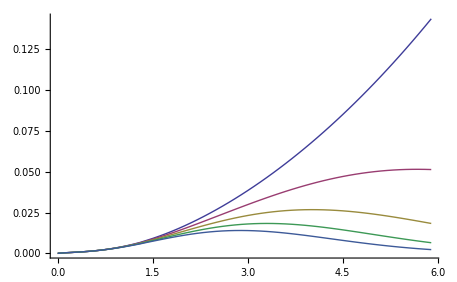

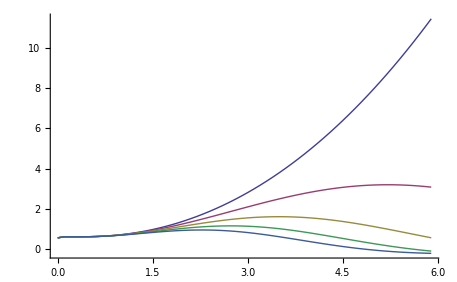

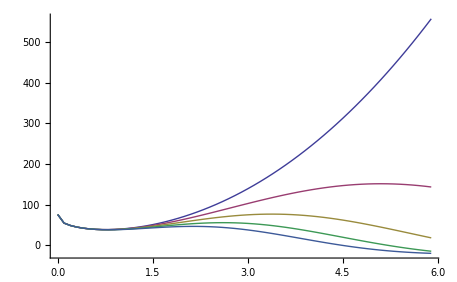

```mathematica
ListPlot[{B1,B2,B3,B4,B5},Joined->True]
ListPlot[{A1,A2,A3,A4,A5},Joined->True]
ListPlot[{C1,C2,C3,C4,C5},Joined->True]
```

```mathematica
Timing[B1=Table[{x,x(CxF[1,2,x,1,C0/bstar[1,1]]+1.2CxFrenormalon[2,x,1,C0/bstar[1,1]])},{x,10^-3,1,0.01}];]
Timing[B2=Table[{x,x(CxF[1,2,x,1,C0/bstar[1,1]]+0CxFrenormalon[2,x,1,C0/bstar[1,1]])},{x,10^-3,1,0.01}];]
Timing[B3=Table[{x,x(CxF[1,2,x,1,C0/bstar[1,1]]-1.2CxFrenormalon[2,x,1,C0/bstar[1,1]])},{x,10^-3,1,0.01}];]
```

{4.25227,Null}

{4.23226,Null}

{4.25227,Null}

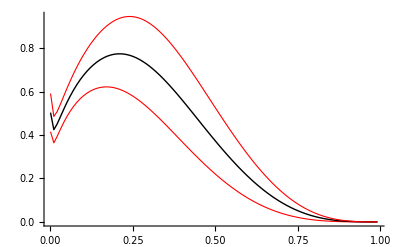

```mathematica
ListPlot[{B1,B2,B3},Joined->True,PlotStyle->{{Thickness[0.002],Red},{Thick,Black},{Thickness[0.002],Red}}]
```

```mathematica
Timing[A1=Table[{bt,(CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.0]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.1,0.0])},{bt,10^-3,10,0.1}];]
Timing[A2=Table[{bt,(CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.03]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.1,0.03])},{bt,10^-3,10,0.1}];]
Timing[A3=Table[{bt,(CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.06]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.1,0.06])},{bt,10^-3,10,0.1}];]
Timing[A4=Table[{bt,(CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.09]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.1,0.09])},{bt,10^-3,10,0.1}];]
Timing[A5=Table[{bt,(CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.12]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.1,0.12])},{bt,10^-3,10,0.1}];]
```

{14.1809,Null}

{17.3891,Null}

{16.761,Null}

{16.593,Null}

{16.281,Null}

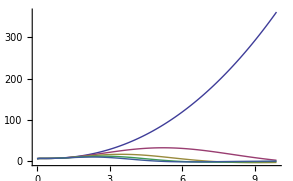

```mathematica
ListPlot[{A1,A2,A3,A4,A5},Joined->True]
```

```mathematica
Timing[A1=Table[{bt,(CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.0]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],0.1,0.0])},{bt,10^-3,10,0.1}];]
Timing[A2=Table[{bt,(CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.03]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],0.1,0.03])},{bt,10^-3,10,0.1}];]
Timing[A3=Table[{bt,(CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.06]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],0.1,0.06])},{bt,10^-3,10,0.1}];]
Timing[A4=Table[{bt,(CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.09]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],0.1,0.09])},{bt,10^-3,10,0.1}];]
Timing[A5=Table[{bt,(CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.12]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],0.1,0.12])},{bt,10^-3,10,0.1}];]
```

{14.2929,Null}

{17.4571,Null}

{16.765,Null}

{16.633,Null}

{16.593,Null}

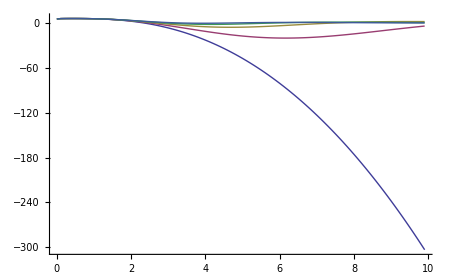

```mathematica
ListPlot[{A1,A2,A3,A4,A5},Joined->True]
```

```mathematica
Timing[R0=Table[{bt,(CxFexp[0,2,0.1,bt,C0/bstar[bt,1],0.09]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.1,0.09])},{bt,10^-3,10,0.1}];]
Timing[R1=Table[{bt,(CxFexp[1,2,0.1,bt,C0/bstar[bt,1],0.09]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.1,0.09])},{bt,10^-3,10,0.1}];]
Timing[R2=Table[{bt,(CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.09]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.1,0.09])},{bt,10^-3,10,0.1}];]
```

{3.84024,Null}

{8.08851,Null}

{16.725,Null}

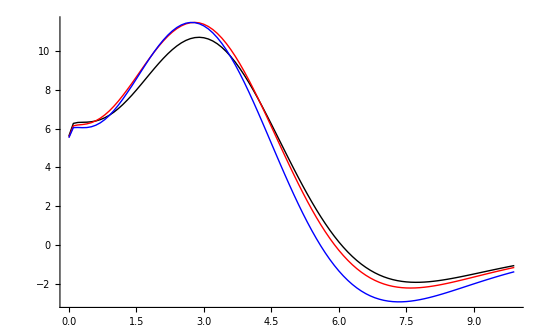

```mathematica
ListPlot[{R0,R1,R2},Joined->True,PlotStyle->{Black,Red,Blue}]
```

```mathematica
Timing[R0=Table[{bt,(CxFexp[0,2,0.1,bt,2,0.09]+CxFrenormalonExp[2,0.1,bt,2,-0.1,0.09])},{bt,10^-3,10,0.1}];]
```

{3.42021,Null}

```mathematica
Timing[R1=Table[{bt,(CxFexp[1,2,0.1,bt,2,0.09]+CxFrenormalonExp[2,0.1,bt,2,-0.1,0.09])},{bt,10^-3,10,0.1}];]
Timing[R2=Table[{bt,(CxFexp[2,2,0.1,bt,2,0.09]+CxFrenormalonExp[2,0.1,bt,2,-0.1,0.09])},{bt,10^-3,10,0.1}];]
```

{7.83249,Null}

{16.741,Null}

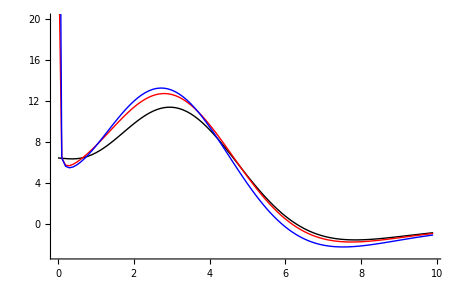

```mathematica
ListPlot[{R0,R1,R2},Joined->True,PlotRange->{-3,20},PlotStyle->{Black,Red,Blue}]
```

```mathematica
Timing[R0=Table[{bt,(CxFexp[0,2,0.1,bt,C0/bstar[bt,1],0.1]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.02,0.1])},{bt,10^-3,10,0.1}];]
Timing[R1=Table[{bt,(CxFexp[1,2,0.1,bt,C0/bstar[bt,1],0.1]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.02,0.1])},{bt,10^-3,10,0.1}];]
Timing[R2=Table[{bt,(CxFexp[2,2,0.1,bt,C0/bstar[bt,1],0.1]+CxFrenormalonExp[2,0.1,bt,C0/bstar[bt,1],-0.02,0.1])},{bt,10^-3,10,0.1}];]
```

{3.81224,Null}

{7.91649,Null}

{16.365,Null}

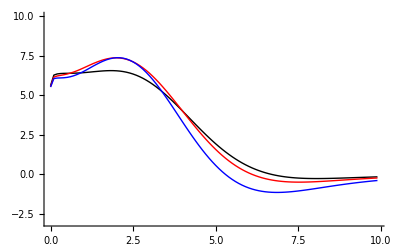

```mathematica
ListPlot[{R0,R1,R2},Joined->True,PlotRange->{-3,10},PlotStyle->{Black,Red,Blue}]
```

```mathematica
?CxF
```

CxF[n_,f_,type_,x_,bt_,μ_] is the leading order of the small-bT expansion for unpolirized TMD PDF.
It is defined as C_(q ← f)(bt,μ)⊗q_f)[x,μ].
The function uses MSTW2008 PDF as input.
n -- pertrubative order of coefficient function,
f -- parton flavour, defined as in MSTW2008, i.e. (-3,-2,-1,0,1,2,3)→ (sbar,ubar,dbar,gluon,d,u,s)
type -- defines inclusion or exclusion of parton mixture, "direct" no parton mixture terms, "withMIX" all terms, "onlyMIX" only mixture terms.
x, bt, μ -- usual TMD variables.
Function CxF[n_,f_,x_,bt_,μ_] evaluates matching without mixing. 
NOTE: parameter ζ is set to ζb (i.e. the ζ-logarithms exponentiated out), NF=3 for all coefficeints, for α_s we take 2-loop definition irrespective pertrubtive order.
ANOTHER NOTE: we use PrecisionGoal→5, since it speeds up the calculation, but far within errorband.

```mathematica
?CxFrenormalonExp
```

CxFrenormalonExp[f_,x_,bt_,μ_,Λ_,g1_,g2_] is the leading renormalon contribution to the quark TMD, without NUMERIC prefactor, with the extra expoenential
It is defined as bt^2g1(*SubscriptBox[(C), (renormalon)])Exp[-x g2 bt^2] ⊗ q.
The discripancy of parameters is taken into account within the renormalon mathing.
The function uses MSTW2008 PDF as input.
f -- parton flavour (can be only quark, or anti quark), defined as in MSTW2008, i.e. (-3,-2,-1,0,1,2,3)→ (sbar,ubar,dbar,gluon,d,u,s)
x, bt, μ -- usual TMD variables.
Λ is the position of Landau pole, to which the divergent series summed. If not specified the 2-loop ΛQCD from the package AlphaStrong is used.

```mathematica
(CxFexp[1,2,0.8,1,10.,0.1]+CxFrenormalonExp[2,0.8,1.,1.,0.3,0.1])
```

-0.0384098

### This is model for u quark from the paper

```mathematica
Needs["PlotLegends`"]
```

```mathematica
MODELu[n_,x_,bt_,μ_,gb_,gq_]:=CxFexp[n,2,x,bt,μ,gb]+CxFrenormalonExp[2,x,bt,μ,0.25,gq,gb]
```

FIGURE 3 LEFT

```mathematica
Timing[R0=Join[Table[{bt,MODELu[0,0.1,bt,C0/bstar[bt,1.5],0.2,0.01]},{bt,10^-3,0.2,0.01}],Table[{bt,MODELu[0,0.1,bt,C0/bstar[bt,1.5],0.2,0.01]},{bt,0.2,8,0.1}]];]
Timing[R1=Join[Table[{bt,MODELu[1,0.1,bt,C0/bstar[bt,1.5],0.2,0.01]},{bt,10^-3,0.2,0.01}],Table[{bt,MODELu[1,0.1,bt,C0/bstar[bt,1.5],0.2,0.01]},{bt,0.2,8,0.1}]];]
Timing[R2=Join[Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0.2,0.01]},{bt,10^-3,0.2,0.01}],Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0.2,0.01]},{bt,0.2,8,0.1}]];]
```

{5.10832,Null}

{10.0966,Null}

{20.5573,Null}

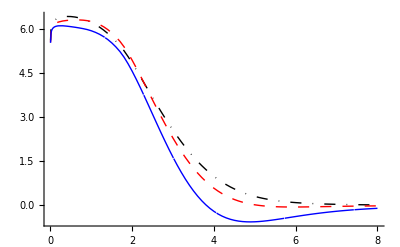

```mathematica
PLOT1=ListPlot[{R0,R1,R2},Joined->True,PlotStyle->{
{Thick,Dashing[{0.02,0.02,0.001,0.02}],Black},
{Thick,Dashing[{0.02,0.02}],Red},
{Thick,Dashing[{1,0}],Blue}
}]
```

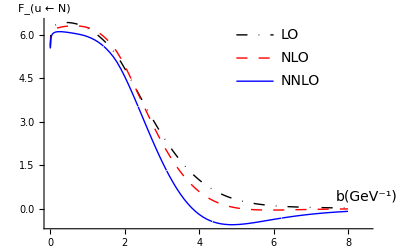

```mathematica
Show[Graphics[{
Text[Style["b(GeV^-1)",FontSize->14],{8.5,0.4}],
{Thick,Dashing[{0.02,0.02,0.001,0.02}],Black,Line[{{5,6},{6,6}}]},
{Thick,Dashing[{0.02,0.02}],Red,Line[{{5,5.2},{6,5.2}}]},
{Thick,Dashing[{1,0}],Blue,Line[{{5,4.4},{6,4.4}}]},
Text[Style["LO",FontSize->14],{6.2,6},{Left,Center}],
Text[Style["NLO",FontSize->14],{6.2,5.2},{Left,Center}],
Text[Style["NNLO",FontSize->14],{6.2,4.4},{Left,Center}]
}]
,PLOT1,
Axes->True,AspectRatio->1/1.6,
AxesLabel->{"",Style["F_(u ← N)",FontSize->14]}]
```

FIGURE 3 RIGHT

```mathematica
Timing[W1=Join[Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,0.5],0.2,0.01]},{bt,10^-3,0.2,0.01}],Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,0.5],0.2,0.01]},{bt,0.2,8,0.1}]];]
Timing[W2=Join[Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.0],0.2,0.01]},{bt,10^-3,0.2,0.01}],Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.0],0.2,0.01]},{bt,0.2,8,0.1}]];]
Timing[W3=Join[Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0.2,0.01]},{bt,10^-3,0.2,0.01}],Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0.2,0.01]},{bt,0.2,8,0.1}]];]
Timing[W4=Join[Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,2.],0.2,0.01]},{bt,10^-3,0.2,0.01}],Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,2.],0.2,0.01]},{bt,0.2,8,0.1}]];]
```

{15.605,Null}

{15.425,Null}

{20.7613,Null}

{20.4533,Null}

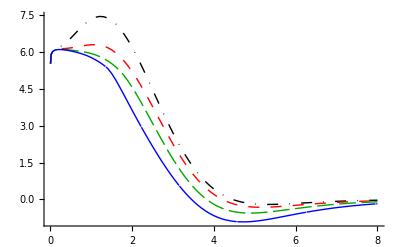

```mathematica
PLOT2=ListPlot[{W1,W2,W3,W4},Joined->True,PlotStyle->{
{Thick,Dashing[{0.02,0.02,0.001,0.02}],Black},
{Thick,Dashing[{0.02,0.02}],Red},
{Thick,Dashing[{0.03,0.01}],Darker@Green},
{Thick,Dashing[{1,0}],Blue}
}]
```

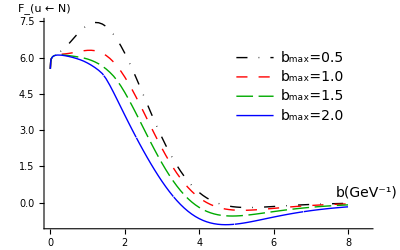

```mathematica
Show[Graphics[{
Text[Style["b(GeV^-1)",FontSize->14],{8.5,0.4}],
{Thick,Dashing[{0.02,0.02,0.001,0.02}],Black,Line[{{5,6},{6,6}}]},
{Thick,Dashing[{0.02,0.02}],Red,Line[{{5,5.2},{6,5.2}}]},
{Thick,Dashing[{0.03,0.01}],Darker@Green,Line[{{5,4.4},{6,4.4}}]},
{Thick,Dashing[{1,0}],Blue,Line[{{5,3.6},{6,3.6}}]},
Text[Style["b_max=0.5",FontSize->14],{6.2,6},{Left,Center}],
Text[Style["b_max=1.0",FontSize->14],{6.2,5.2},{Left,Center}],
Text[Style["b_max=1.5",FontSize->14],{6.2,4.4},{Left,Center}],
Text[Style["b_max=2.0",FontSize->14],{6.2,3.6},{Left,Center}]
}]
,PLOT2,
Axes->True,AspectRatio->1/1.6,
AxesLabel->{"",Style["F_(u ← N)",FontSize->14]}]
```

FIGURE 4 LEFT

```mathematica
Timing[Y1=Join[Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0.2,0.1]},{bt,10^-3,0.2,0.01}],Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0.2,0.1]},{bt,0.2,8,0.1}]];]
Timing[Y2=Join[Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0.2,0.001]},{bt,10^-3,0.2,0.01}],Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0.2,0.001]},{bt,0.2,8,0.1}]];]
Timing[Y3=Join[Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0.2,-0.1]},{bt,10^-3,0.2,0.01}],Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0.2,-0.1]},{bt,0.2,8,0.1}]];]
```

{20.9613,Null}

{20.6733,Null}

{20.6973,Null}

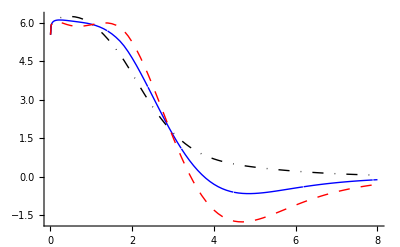

```mathematica
PLOT3=ListPlot[{Y1,Y2,Y3},Joined->True,PlotStyle->{
{Thick,Dashing[{0.02,0.02,0.001,0.02}],Black},
{Thick,Dashing[{1,0}],Blue},
{Thick,Dashing[{0.02,0.02}],Red}
}]
```

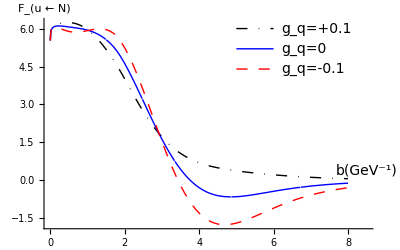

```mathematica
Show[Graphics[{
Text[Style["b(GeV^-1)",FontSize->14],{8.5,0.4}],
{Thick,Dashing[{0.02,0.02,0.001,0.02}],Black,Line[{{5,6},{6,6}}]},
{Thick,Dashing[{1,0}],Blue,Line[{{5,5.2},{6,5.2}}]},
{Thick,Dashing[{0.02,0.02}],Red,Line[{{5,4.4},{6,4.4}}]},
Text[Style["g_q=+0.1",FontSize->14],{6.2,6},{Left,Center}],
Text[Style["g_q=0",FontSize->14],{6.2,5.2},{Left,Center}],
Text[Style["g_q=-0.1",FontSize->14],{6.2,4.4},{Left,Center}]
}]
,PLOT3,
Axes->True,AspectRatio->1/1.6,
AxesLabel->{"",Style["F_(u ← N)",FontSize->14]}]
```

FIGURE 4 RIGHT

```mathematica
Timing[U1=Join[Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0.3,0.01]},{bt,10^-3,0.2,0.01}],Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0.3,0.01]},{bt,0.2,8,0.1}]];]
Timing[U2=Join[Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0.2,0.01]},{bt,10^-3,0.2,0.01}],Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0.2,0.01]},{bt,0.2,8,0.1}]];]
Timing[U3=Join[Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0.1,0.01]},{bt,10^-3,0.2,0.01}],Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0.1,0.01]},{bt,0.2,8,0.1}]];]
Timing[U4=Join[Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0.01,0.01]},{bt,10^-3,0.2,0.01}],Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0.01,0.01]},{bt,0.2,8,0.1}]];]
```

{19.6932,Null}

{20.6373,Null}

{21.9854,Null}

{20.1133,Null}

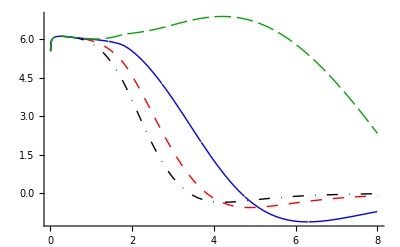

```mathematica
PLOT4=ListPlot[{U1,U2,U3,U4},Joined->True,PlotStyle->{
{Thick,Dashing[{0.02,0.02,0.001,0.02}],Black},
{Thick,Dashing[{0.02,0.02}],Red},
{Thick,Dashing[{1,0}],Blue},
{Thick,Dashing[{0.03,0.01}],Darker@Green}
}]
```

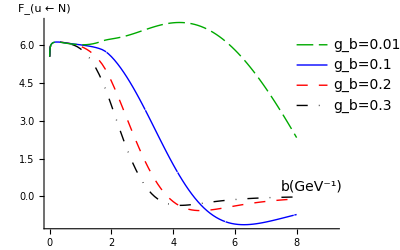

```mathematica
Show[Graphics[{
Text[Style["b(GeV^-1)",FontSize->14],{8.5,0.4}],
{Thick,Dashing[{0.03,0.01}],Darker@Green,Line[{{5+3,6},{6+3,6}}]},
{Thick,Dashing[{1,0}],Blue,Line[{{5+3,5.2},{6+3,5.2}}]},
{Thick,Dashing[{0.02,0.02}],Red,Line[{{5+3,4.4},{6+3,4.4}}]},
{Thick,Dashing[{0.02,0.02,0.001,0.02}],Black,Line[{{5+3,3.6},{6+3,3.6}}]},
Text[Style["g_b=0.01",FontSize->14],{6.2+3,6},{Left,Center}],
Text[Style["g_b=0.1",FontSize->14],{6.2+3,5.2},{Left,Center}],
Text[Style["g_b=0.2",FontSize->14],{6.2+3,4.4},{Left,Center}],
Text[Style["g_b=0.3",FontSize->14],{6.2+3,3.6},{Left,Center}]
}]
,PLOT4,
Axes->True,AspectRatio->1/1.6,
AxesLabel->{"",Style["F_(u ← N)",FontSize->14]}]
```

FIGURE 5

```mathematica
Xvalues=Table[Exp[-x]-10^-6,{x,0.,7,0.01}];
```

```mathematica
Timing[X1=Table[{x,x MODELu[2,x,1.5,C0/bstar[1.5,1.5],0.2,0.1]},{x,Xvalues}];]
Timing[X2=Table[{x,x MODELu[2,x,1.5,C0/bstar[1.5,1.5],0.2,0.001]},{x,Xvalues}];]
Timing[X3=Table[{x,x MODELu[2,x,1.5,C0/bstar[1.5,1.5],0.2,-0.1]},{x,Xvalues}];]
```

{150.849,Null}

{150.057,Null}

{150.317,Null}

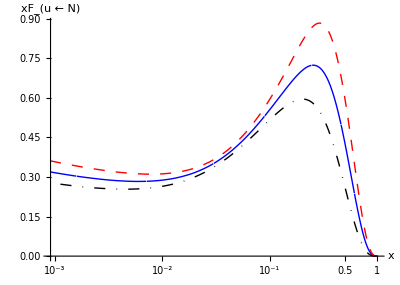

```mathematica
PLOT5=ListLogLinearPlot[{X1,X2,X3},Joined->True,PlotStyle->{
{Thick,Dashing[{0.02,0.02,0.001,0.02}],Black},
{Thick,Dashing[{1,0}],Blue},
{Thick,Dashing[{0.02,0.02}],Red}
},
AxesLabel->{Style["x",FontSize->14],Style["xF_(u ← N)",FontSize->14]},
Ticks->{{1,0.5,{0.1,"10^-1"},{0.01,"10^-2"},{0.001,"10^-3",0.03}},Automatic},
 PlotLegend->{"g_q=0.1", "g_q=0.", "g_q=-0.1"},
LegendPosition->{.7,0.2},LegendSize->0.5, LegendShadow->None,LegendBorder->None,
AspectRatio->1/1.4
]
```

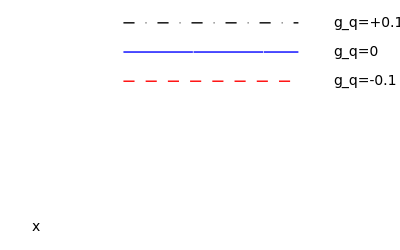

```mathematica
Show[Graphics[{
Text[Style["x",FontSize->14],{8.5,0.4}],
{Thick,Dashing[{0.02,0.02,0.001,0.02}],Black,Line[{{5+4,6},{6+4,6}}]},
{Thick,Dashing[{1,0}],Blue,Line[{{5+4,5.2},{6+4,5.2}}]},
{Thick,Dashing[{0.02,0.02}],Red,Line[{{5+4,4.4},{6+4,4.4}}]},
Text[Style["g_q=+0.1",FontSize->14],{6.2+4,6},{Left,Center}],
Text[Style["g_q=0",FontSize->14],{6.2+4,5.2},{Left,Center}],
Text[Style["g_q=-0.1",FontSize->14],{6.2+4,4.4},{Left,Center}]
}],AspectRatio->1/1.6]
```

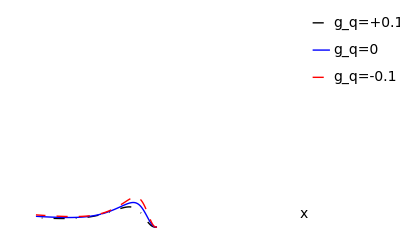

```mathematica
Show[%107,%105]
```

#### Plot for QCD evol 2016 proceedings

```mathematica
Timing[R0=Join[Table[{bt,MODELu[0,0.1,bt,C0/bstar[bt,1.5],0,0.00000000001]},{bt,10^-3,0.2,0.01}],Table[{bt,MODELu[0,0.1,bt,C0/bstar[bt,1.5],0,0.0000000001]},{bt,0.2,8,0.1}]];]
Timing[R1=Join[Table[{bt,MODELu[1,0.1,bt,C0/bstar[bt,1.5],0,0.00000000001]},{bt,10^-3,0.2,0.01}],Table[{bt,MODELu[1,0.1,bt,C0/bstar[bt,1.5],0,0.00000000001]},{bt,0.2,8,0.1}]];]
Timing[R2=Join[Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0,0.00000000001]},{bt,10^-3,0.2,0.01}],Table[{bt,MODELu[2,0.1,bt,C0/bstar[bt,1.5],0,0.00000000001]},{bt,0.2,8,0.1}]];]
```

{3.90424,Null}

{8.54453,Null}

{18.3851,Null}

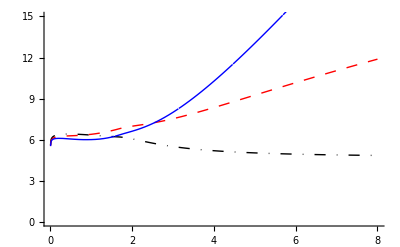

```mathematica
PLOT1=ListPlot[{R0,R1,R2},Joined->True,PlotStyle->{
{Thick,Dashing[{0.02,0.02,0.001,0.02}],Black},
{Thick,Dashing[{0.02,0.02}],Red},
{Thick,Dashing[{1,0}],Blue}
},PlotRange->{0,15}]
```

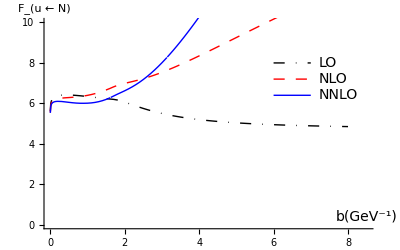

```mathematica
With[{a=1,b=2},Show[Graphics[{
Text[Style["b(GeV^-1)",FontSize->14],{8.5,0.4}],
{Thick,Dashing[{0.02,0.02,0.001,0.02}],Black,Line[{{5+a,6+b},{6+a,6+b}}]},
{Thick,Dashing[{0.02,0.02}],Red,Line[{{5+a,5.2+b},{6+a,5.2+b}}]},
{Thick,Dashing[{1,0}],Blue,Line[{{5+a,4.4+b},{6+a,4.4+b}}]},
Text[Style["LO",FontSize->14],{6.2+a,6+b},{Left,Center}],
Text[Style["NLO",FontSize->14],{6.2+a,5.2+b},{Left,Center}],
Text[Style["NNLO",FontSize->14],{6.2+a,4.4+b},{Left,Center}]
}]
,PLOT1,
Axes->True,AspectRatio->1/1.6,
AxesLabel->{"",Style["F_(u ← N)",FontSize->14]},PlotRange->{0,10}]]
```